Learning from the previous discussion (1)(2) about hat tiles, we can easily study other polygon tiles with similar idea by grow function, especially other relatives of the hat tile. Here we try to study the promising vertex configurations for “spectre tile”, which is notated as Tile(1,1) in the original paper while hat tile is Tile(1,√3). The reason will be shown later here.

# Tile Family Introduction

The hat tile has three different length of edges - 1, 2 and √3. In fact, there is only one edge of length 2, which is the longest edge of the hat tile. We can turn hat tile from 13-polygon into 14-polygon by splitting its longest edge into two on its middle point, which adds one more vertex with angle 1/2 (Pi). Then, two arguments of edge length can determine a shape of tile as following:

```mathematica
Manipulate[
Labeled[
Graphics[
{
LightGreen,
EdgeForm[Black],
Tile[{m,n}][{0,0},0,False,1]
}
],StringJoin["Ratio m/n=",ToString[m/n]],Top
],
{m,0,2},
{n,0,2},
SaveDefinitions->True
]
```

And there is a family of this kind of tiles:

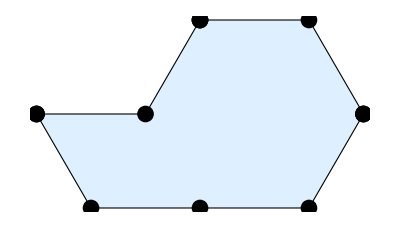
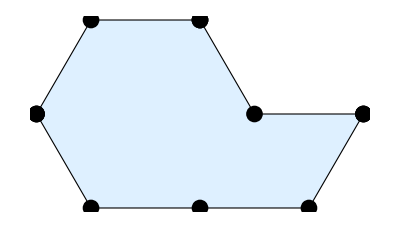
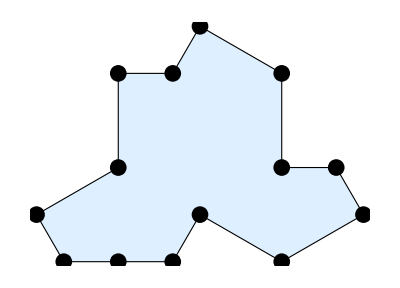
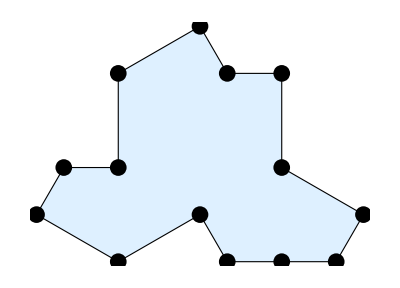
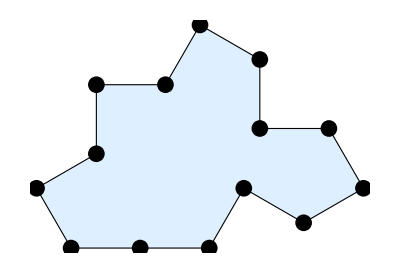
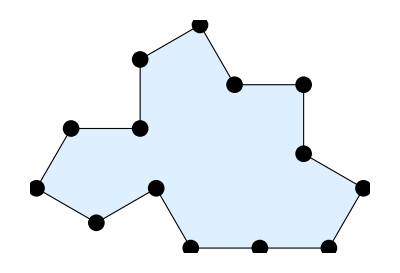
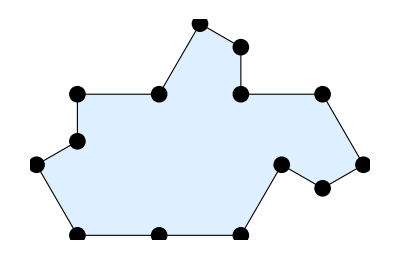
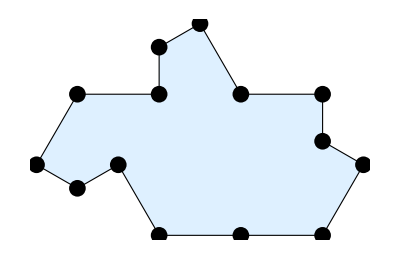
-Graphics-Tile(1,0) | -Graphics-Tile(1,0) | -Graphics-Tile(1,√3) | -Graphics-Tile(1,√3) | -Graphics-Tile(1,1) | -Graphics-Tile(1,1)
-Graphics-Tile(√3,1) | -Graphics-Tile(√3,1) | -Graphics-Tile(0,1) | -Graphics-Tile(0,1) |  |

```mathematica
Grid[
Partition[
MapThread[
Labeled[
Graphics[
{
LightBlue,EdgeForm[Black],
Tile[#1][{0,0},0,#2,1],
PointSize[0.03],
Black,
Point[TileVertices[#1][{0,0},0,#2,1]]
}
],
TraditionalForm[Tile@@#1],Bottom
]&,
{
{
{1,0},{1,0},{1,Sqrt[3]},{1,Sqrt[3]},{1,1},{1,1},
{Sqrt[3],1},{Sqrt[3],1},{0,1},{0,1}
}
,
{False,True,False,True,False,True,
False,True,False,True
}
}],UpTo[6]],Frame->All,FrameStyle->LightGray,ImageSize->Full
]
```

The Tile(1,0) and Tile(0,1) are degenerate since edge length zero causing some of the vertices merge together. Tile(1,√3) is the hat tile and Tile(1,1) is the spectre. Additionally, Tile(√3,1) is another interesting tile named “turtle”.

According to the original paper, Tile(1,1), which is the “spectre”, admits more vertex configurations since two equal length of edges. Permitting reflection, Tile(1,1) can tile the plane periodically or aperiodically, but if reflection is forbidden, it only admits aperiodic tilings.

Here we are going to study the vertex configurations of Tile(1,1) “Spectre” when reflected tiles are forbidden:

# Basic Study

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["HappyTile.wl"]
```

The idea is the same as what we did to hat tiles in the previous discussion (1)(2). Here are the details:

## 1/3+1/3+1/3

```mathematica
oneThirdVertices
```

{2,4,6,12,14}

```mathematica
cases=Tuples[{oneThirdVertices,Range[0,11],oneThirdVertices}];
```

```mathematica
cases={{{0,0},0,False,#1},{{0,0},#2,False,#3}}&@@@cases;
```

```mathematica
res1=With[
{
res=PlanarPolygonFragmentation@@(spectre@@@({#1,#2}&@@#))
},
If[Total[Length/@res]==3,#,Nothing]
]&/@cases;
```

```mathematica
res1//Length
```

77

```mathematica
pointToAngle = Association[{
	1->{12,1,2,3,4,5,6,7,8},
	2->{2,3,4,5},
	3->{5,6,7},
	4->{7,8,9,10},
	5->{4,5,6,7,8,9,10,11,12},
	6->{6,7,8,9},
	7->{9,10,11},
	8->{7,8,9,10,11,12,1,2},
	9->{10,11,12},
	10->{8,9,10,11,12,1,2,3},
	11->{11,12,1},
	12->{1,2,3,4},
	13->{1,2,3,4,5,6},
	14->{3,4,5,6}
}];
getPointsOccupation[tile_] := Mod[(1-2Boole[#2])(pointToAngle[#3]+#1)+7(Boole[#2]),12,1]&@@tile/;Length[tile]==3
getPointsOccupation[tile_] := Mod[(1-2Boole[#2])(pointToAngle[#3]+#1)+7(Boole[#2]),12,1]&@@tile[[2;;]]/;Length[tile]==4
```

```mathematica
clusterPoints=Function[list,
Block[{p},
If[list==Range[12],
{Range[12]},DeleteDuplicates[MapThread[Union,{Most[NestWhileList[Mod[#+1,12,1]&,#,MemberQ[list,#]&]]&/@list,Most[NestWhileList[Mod[#-1,12,1]&,#,MemberQ[list,#]&]]&/@list}],#1==#2&]]]];
```

```mathematica
res2=Select[res1,
AllTrue[Length/@clusterPoints[Complement[Range[12],Union@@(getPointsOccupation/@#)]],#>=3&]&];
```

```mathematica
res3=Union[##,SameTest->(Sort[#1]==Sort[#2]&)]&@@
Outer[
If[IntersectingQ[Union@@(getPointsOccupation/@#1),getPointsOccupation[#2]],Nothing,Append[#1,#2]]&,
res2
,
Tuples[{{{0,0}},Range[0,11],{False},oneThirdVertices}],
1
];
```

```mathematica
res3//Length
```

112

```mathematica
AbsoluteTiming[
res4=If[
AllTrue[PlanarPolygonFragmentation@@@Subsets[spectre@@@#,{2}],Total[Length/@#]==3&],
#,
Nothing
]&/@
res3;
]
```

{11.6624,Null}

```mathematica
res4//Length
```

20

```mathematica
res5=DeleteDuplicates[res4,MemberQ[Sort[Sort/@allRoatationsofTiles[#1[[All,2;;]]]],Sort[#2[[All,2;;]]]]&];
```

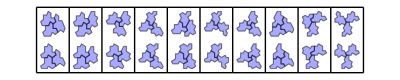

```mathematica
GraphicsGrid[Transpose[{show[#,step->{1,1}],show[#]}&/@res5],ImageSize->Full,Frame->{All,False}]
```

It’s the same as the result of hat tile.

```mathematica
Iconize[res5]
```

```mathematica
[[All,All,2;;]]
```

{{{0,False,2},{0,False,6},{4,False,6}},{{0,False,2},{0,False,6},{8,False,2}},{{0,False,2},{4,False,2},{8,False,2}},{{0,False,4},{2,False,12},{4,False,4}},{{0,False,4},{2,False,12},{8,False,14}},{{0,False,4},{2,False,12},{10,False,12}},{{0,False,4},{4,False,4},{8,False,4}},{{0,False,6},{4,False,6},{8,False,6}},{{0,False,12},{2,False,14},{8,False,12}},{{0,False,12},{4,False,12},{8,False,12}}}

## 1/4+1/4+1/2

```mathematica
oneFourthVertices
```

{3,7,9,11}

```mathematica
oneHalfVertices
```

{13}

```mathematica
fixedTile={0,False,13};
```

```mathematica
getPointsOccupation[fixedTile]
```

{1,2,3,4,5,6}

```mathematica
allStateForOneTile=Tuples[{Range[0,11],{False},oneFourthVertices}];
```

```mathematica
res1=Select[allStateForOneTile,SubsetQ[Range[7,12],getPointsOccupation[#]]&];
res1//Length
```

16

```mathematica
res2=Select[{#,fixedTile}&/@res1,AllTrue[Length/@clusterPoints[Complement[Range[12],Union@@(getPointsOccupation/@#)]],#>=3&]&];
res2//Length
```

8

```mathematica
res2[[1]]
```

{{0,False,9},{0,False,13}}

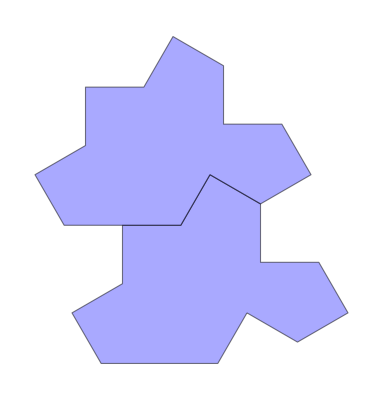
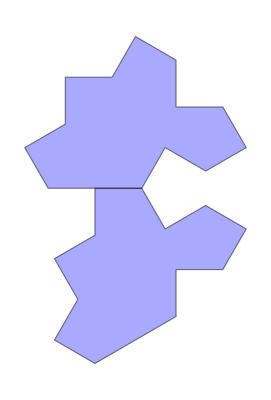
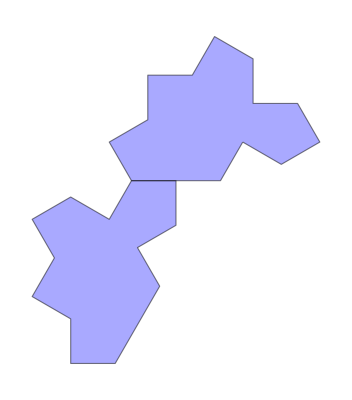
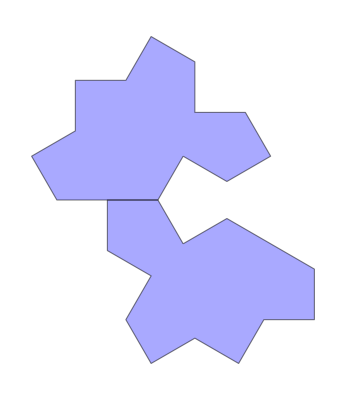
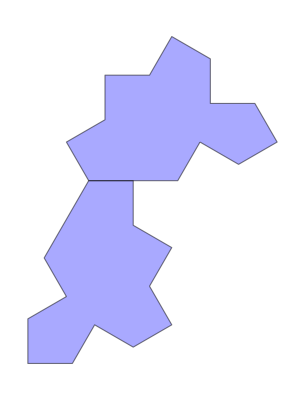
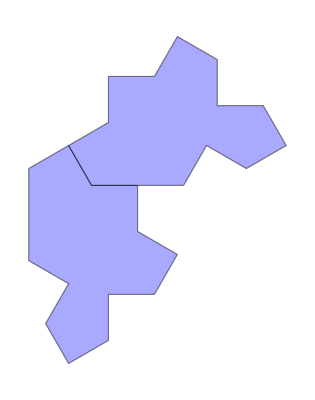
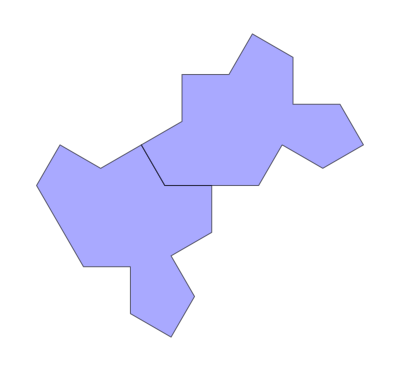
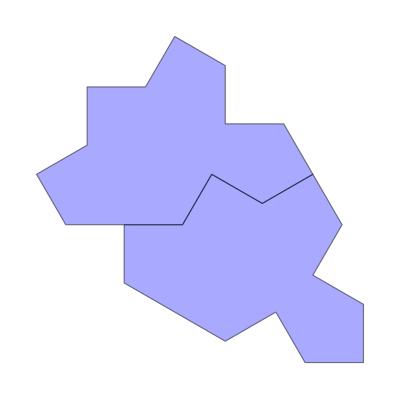

```mathematica
show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,res2,{2}]
```

Obvious 2,4 is invalid because of the hole.

```mathematica
res3=Drop[res2,{2,4,2}];
```

```mathematica
res4=Join@@(
Function[state,
Append[state,#]&/@
Select[
allStateForOneTile,
SubsetQ[
Complement[Range[12],Union@@getPointsOccupation/@state],
getPointsOccupation[#]]&
]
]/@res3
);
res4//Length
```

24

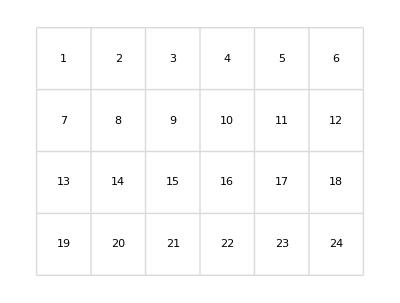

```mathematica
GraphicsGrid[
Partition[
Labeled[
show[Map[Prepend[#,{0,0}]&,res4[[#]]],step->{1,1}],
#,Left]&/@Range[Length[res4]],
UpTo[6]
],
ImageSize->Full,Frame->All,FrameStyle->LightGray]
```

delete intersection and invalid concave cases:2,3,6,7,9,10,11,13,14,15,18,19. And delete same cases with code of different order.

```mathematica
res5=res4[[Complement[Range[Length[res4]],{2,3,6,7,9,10,11,13,14,15,18,19}]]];
res5=DeleteDuplicatesBy[res5,Sort];
res5//Length
```

6

There are more cases than hat tiles. Lets compare:

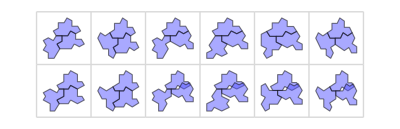

```mathematica
GraphicsGrid[
Transpose[
{
show[Map[Prepend[#,{0,0}]&,#],step->{1,1}],
show[Map[Prepend[#,{0,0}]&,#],step->{1,Sqrt[3]}]
}&/@res5
],
ImageSize->Full,Frame->All,FrameStyle->LightGray]
```

There are only two valid cases for hat tile but six for spectre tile, since with ratio (1,1) more possible “T” can be formed without intersection.

```mathematica
Iconize[res5]
```

## 1/4+1/4+1/4+1/4

#### Main study

Try to construct all angle valid cases:

```mathematica
allStateofOneTile=Tuples[{Range[0,11],{False},oneFourthVertices}];
```

```mathematica
pointsToStates=GroupBy[allStateofOneTile,getPointsOccupation]
```

<|{5,6,7}→{{0,False,3},{6,False,11},{7,False,9},{8,False,7}},{9,10,11}→{{0,False,7},{4,False,3},{10,False,11},{11,False,9}},{10,11,12}→{{0,False,9},{1,False,7},{5,False,3},{11,False,11}},{11,12,1}→{{0,False,11},{1,False,9},{2,False,7},{6,False,3}},{6,7,8}→{{1,False,3},{7,False,11},{8,False,9},{9,False,7}},{12,1,2}→{{1,False,11},{2,False,9},{3,False,7},{7,False,3}},{7,8,9}→{{2,False,3},{8,False,11},{9,False,9},{10,False,7}},{1,2,3}→{{2,False,11},{3,False,9},{4,False,7},{8,False,3}},{8,9,10}→{{3,False,3},{9,False,11},{10,False,9},{11,False,7}},{2,3,4}→{{3,False,11},{4,False,9},{5,False,7},{9,False,3}},{3,4,5}→{{4,False,11},{5,False,9},{6,False,7},{10,False,3}},{4,5,6}→{{5,False,11},{6,False,9},{7,False,7},{11,False,3}}|>

According to the angle, get all possible combinations.

```mathematica
cases=Tuples[{
pointsToStates[{11,12,1}],
pointsToStates[{2,3,4}],
pointsToStates[{5,6,7}],
pointsToStates[{8,9,10}]
}
];
cases//Length
```

256

Delete rotation equivalent cases

```mathematica
res1=DeleteDuplicates[cases,MemberQ[Sort[Sort/@allRoatationsofTiles[#1]],Sort[#2]]&];
res1//Length
```

70

Delete intersection cases:

```mathematica
res2=Select[res1,And@@(
Apply[
Total[Length/@PlanarPolygonFragmentation[#1,#2]]==3&,
Subsets[spectre@@@(Prepend[#,{0,0}]&/@#),{2}],
{1}
]
)&];
```

```mathematica
res2//Length
```

24

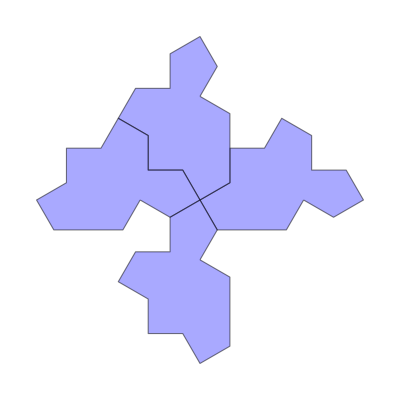
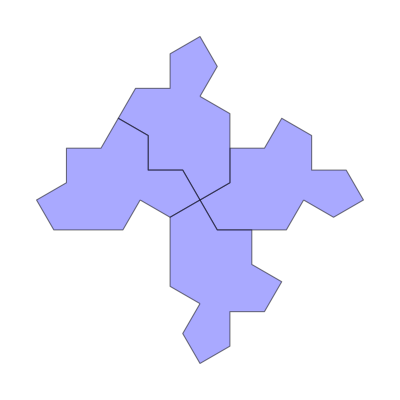
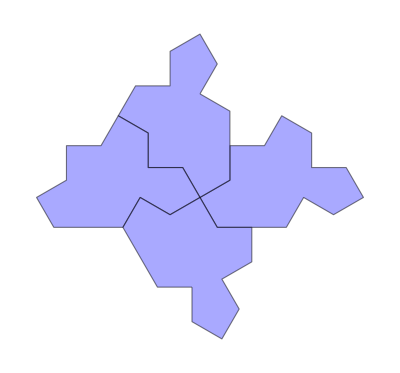
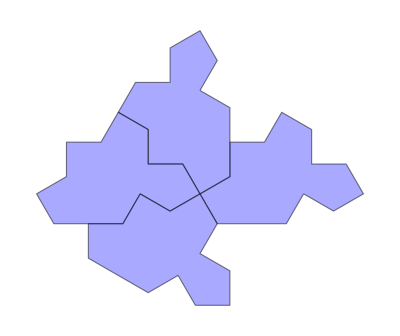
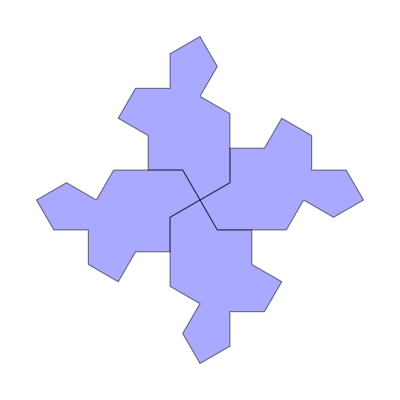
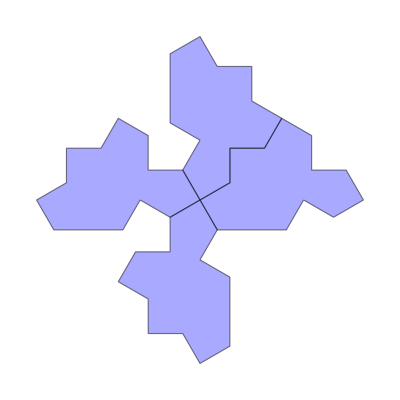
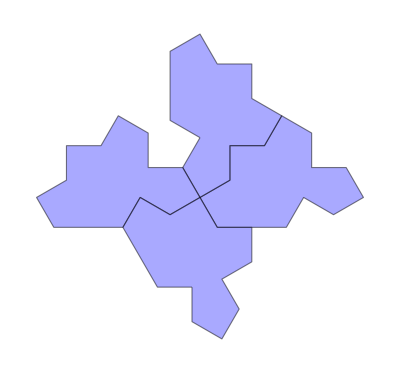
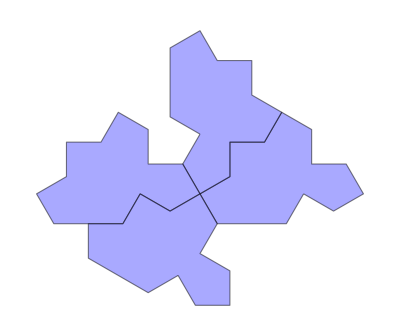
-Graphics-1 | -Graphics-2 | -Graphics-3 | -Graphics-4 | -Graphics-5 | -Graphics-6
-Graphics-7 | -Graphics-8 | -Graphics-9 | -Graphics-10 | -Graphics-11 | -Graphics-12
-Graphics-13 | -Graphics-14 | -Graphics-15 | -Graphics-16 | -Graphics-17 | -Graphics-18
-Graphics-19 | -Graphics-20 | -Graphics-21 | -Graphics-22 | -Graphics-23 | -Graphics-24

```mathematica
Grid[
Partition[
MapThread[Labeled[
show[#1,step->{1,1}],
#2]&,
{
Map[Prepend[#,{0,0}]&,res2,{2}],
Range[Length[res2]]
}],
6],Frame->All
]
```

1,6,7,8,11,14,15,17,19,20,22,23,24 are invalid because of the impossible hole.

```mathematica
res3=res2[[Complement[Range[Length[res2]],{1,6,7,8,11,14,15,17,19,20,22,23,24}]]];
res3//Length
```

11

```mathematica
Grid[
Partition[
MapThread[Labeled[
show[#1,step->{1,1}],
#2]&,
{
Map[Prepend[#,{0,0}]&,res3,{2}],
Range[Length[res3]]
}],
UpTo[6]],Frame->All
]
```

-Graphics-1 | -Graphics-2 | -Graphics-3 | -Graphics-4 | -Graphics-5 | -Graphics-6
-Graphics-7 | -Graphics-8 | -Graphics-9 | -Graphics-10 | -Graphics-11 |

#### For the 1st case:

```mathematica
state=Prepend[#,{0,0}]&/@res3[[1]];
```

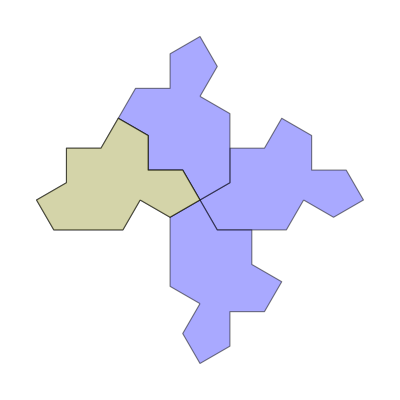

```mathematica
show[state[[{3}]],state,step->{1,1}]
```

```mathematica
getVertexInformation[{1,1}][(turtleVertices@@state[[3]])[[2]],state]
```

{{{-(√3)/2,-1/2},0,False,2},{{-(√3)/2,-1/2},9,False,12}}

Look up 1/3 vertex conclusion

```mathematica
[[All,All,4]]
```

{{2,6,6},{2,6,2},{2,2,2},{4,12,4},{4,12,14},{4,12,12},{4,4,4},{6,6,6},{12,14,12},{12,12,12}}

There’s no sets including {2,12}, so this case is invalid.

#### For the 3nd case

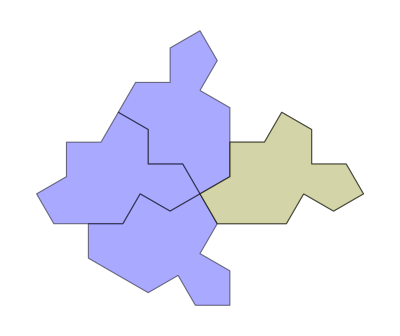

```mathematica
state=Prepend[#,{0,0}]&/@res3[[3]];
show[state[[{1}]],state,step->{1,1}]
```

```mathematica
getVertexInformation[{1,1}][(turtleVertices@@state[[1]])[[-3]],state]
```

{{{1/2,-(√3)/2},0,False,12},{{1/2,-(√3)/2},11,False,6}}

Same as before, it’s invalid.

#### 5th case

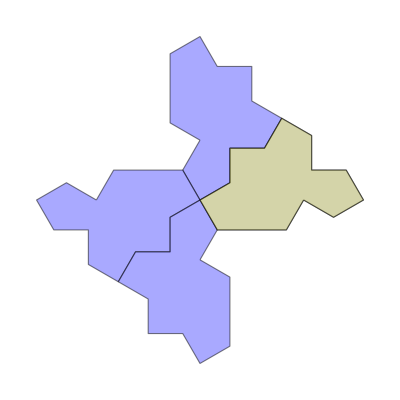

```mathematica
state=Prepend[#,{0,0}]&/@res3[[5]];
show[state[[{1}]],state,step->{1,1}]
```

```mathematica
getVertexInformation[{1,1}][(turtleVertices@@state[[1]])[[-3]],state]
```

{{{1/2,-(√3)/2},0,False,12},{{1/2,-(√3)/2},3,False,2}}

Same invlaid.

#### 6th case

same as 5th.

#### 8th case

same as 3nd case.

#### result

```mathematica
res4=res3[[Complement[Range[Length[res3]],{1,3,5,6,8}]]];
```

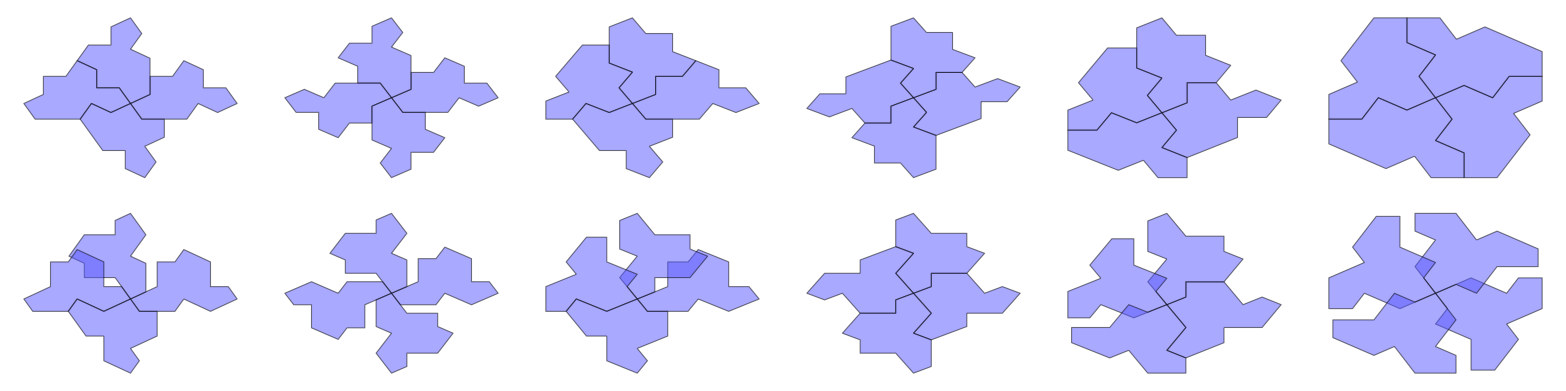

```mathematica
Grid[
Transpose[
Map[
{
show[#,step->{1,1}],
show[#,step->{1,Sqrt[3]}]
}&,
Map[Prepend[#,{0,0}]&,res4,{2}]
]
],
Frame->{All,False}
]
```

It can be seen that Tile(1,1) admits more valid combinations than hat tiles in terms of intersection and local validity.

Result is shown below:

{{{0,False,11},{3,False,11},{0,False,3},{10,False,9}},{{0,False,11},{3,False,11},{6,False,11},{9,False,11}},{{0,False,11},{9,False,3},{8,False,7},{10,False,9}},{{1,False,9},{9,False,3},{7,False,9},{3,False,3}},{{1,False,9},{9,False,3},{8,False,7},{11,False,7}},{{2,False,7},{5,False,7},{8,False,7},{11,False,7}}}

## 1/2+1/2

```mathematica
oneHalfVertices
```

{13}

There is only one valid configuration for 1/2+1/2, which is pretty simple.

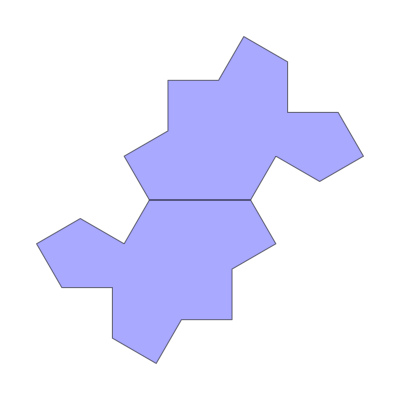

```mathematica
show[
{
{{0,0},0,False,13},
{{0,0},6,False,13}
},
step->{1,1}
]
```

## 1/3+2/3

```mathematica
twoThirdVertices
```

{8,10}

```mathematica
cases=Tuples[{Range[0,11],{False},twoThirdVertices}];
```

```mathematica
pointsToStates=GroupBy[cases,getPointsOccupation]
```

<|{7,8,9,10,11,12,1,2}→{{0,False,8},{11,False,10}},{8,9,10,11,12,1,2,3}→{{0,False,10},{1,False,8}},{9,10,11,12,1,2,3,4}→{{1,False,10},{2,False,8}},{10,11,12,1,2,3,4,5}→{{2,False,10},{3,False,8}},{11,12,1,2,3,4,5,6}→{{3,False,10},{4,False,8}},{12,1,2,3,4,5,6,7}→{{4,False,10},{5,False,8}},{1,2,3,4,5,6,7,8}→{{5,False,10},{6,False,8}},{2,3,4,5,6,7,8,9}→{{6,False,10},{7,False,8}},{3,4,5,6,7,8,9,10}→{{7,False,10},{8,False,8}},{4,5,6,7,8,9,10,11}→{{8,False,10},{9,False,8}},{5,6,7,8,9,10,11,12}→{{9,False,10},{10,False,8}},{6,7,8,9,10,11,12,1}→{{10,False,10},{11,False,8}}|>

```mathematica
allStateForOneTile=Tuples[{Range[0,11],{False},oneThirdVertices}];
```

```mathematica
as=Association[#->Function[
usedPoints,
Select[allStateForOneTile,IntersectingQ[getPointsOccupation[#],usedPoints]==False&]
][#]&/@Keys[pointsToStates]];
```

```mathematica
res1=Union[##,SameTest->(Sort[#1]==Sort[#2]&)]&@@(Tuples[{pointsToStates[#],as[#]}]&/@Keys[as]);
```

```mathematica
res1//Length
```

120

```mathematica
res2=DeleteDuplicates[res1,MemberQ[Sort[Sort/@allRoatationsofTiles[#1]],Sort[#2]]&];
res2//Length
```

10

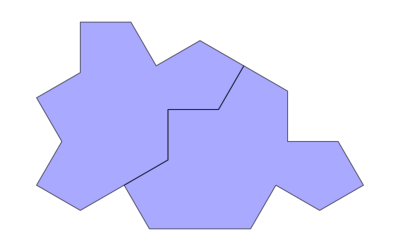
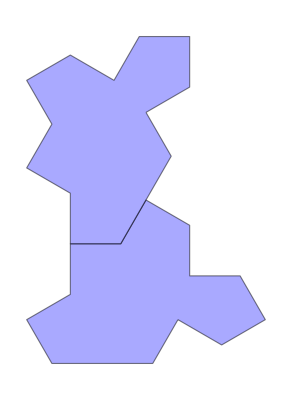
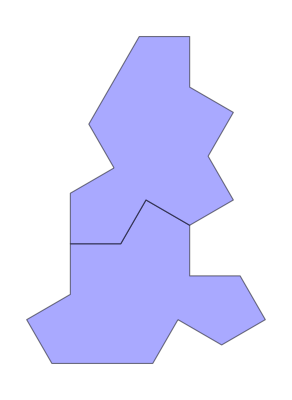
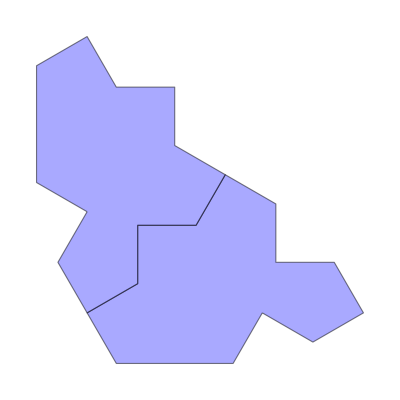
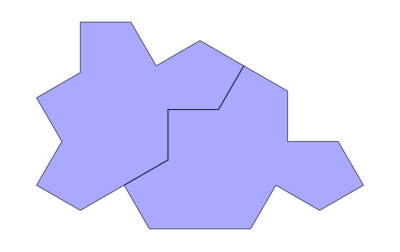
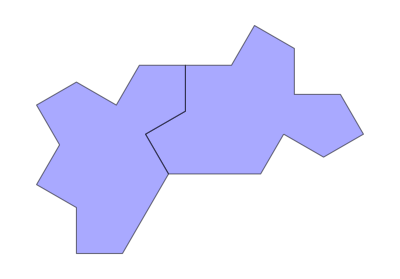
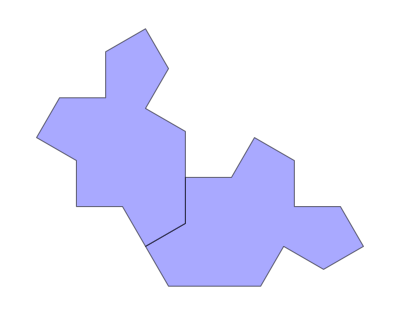
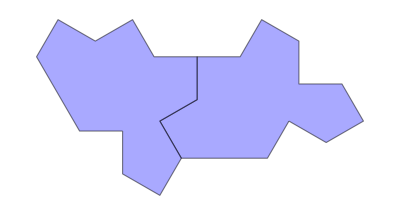
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
show[Prepend[#,{0,0}]&/@#,step->{1,1}]&/@res2
```

```mathematica
Iconize[res2]
```

## 1/4+3/4

```mathematica
threeFourthVertices
```

{1,5}

```mathematica
cases=Tuples[{Range[0,11],{False},threeFourthVertices}];
```

```mathematica
pointsToStates=GroupBy[cases,getPointsOccupation]
```

<|{12,1,2,3,4,5,6,7,8}→{{0,False,1},{8,False,5}},{4,5,6,7,8,9,10,11,12}→{{0,False,5},{4,False,1}},{1,2,3,4,5,6,7,8,9}→{{1,False,1},{9,False,5}},{5,6,7,8,9,10,11,12,1}→{{1,False,5},{5,False,1}},{2,3,4,5,6,7,8,9,10}→{{2,False,1},{10,False,5}},{6,7,8,9,10,11,12,1,2}→{{2,False,5},{6,False,1}},{3,4,5,6,7,8,9,10,11}→{{3,False,1},{11,False,5}},{7,8,9,10,11,12,1,2,3}→{{3,False,5},{7,False,1}},{8,9,10,11,12,1,2,3,4}→{{4,False,5},{8,False,1}},{9,10,11,12,1,2,3,4,5}→{{5,False,5},{9,False,1}},{10,11,12,1,2,3,4,5,6}→{{6,False,5},{10,False,1}},{11,12,1,2,3,4,5,6,7}→{{7,False,5},{11,False,1}}|>

```mathematica
allStateForOneTile=Tuples[{Range[0,11],{False},oneFourthVertices}];
```

```mathematica
as=Association[#->Function[
usedPoints,
Select[allStateForOneTile,IntersectingQ[getPointsOccupation[#],usedPoints]==False&]
][#]&/@Keys[pointsToStates]];
```

```mathematica
res1=Union[##,SameTest->(Sort[#1]==Sort[#2]&)]&@@(Tuples[{pointsToStates[#],as[#]}]&/@Keys[as]);
```

```mathematica
res1//Length
```

96

```mathematica
res2=DeleteDuplicates[res1,MemberQ[Sort[Sort/@allRoatationsofTiles[#1]],Sort[#2]]&];
res2//Length
```

8

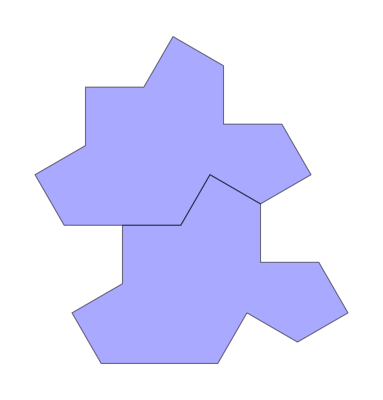
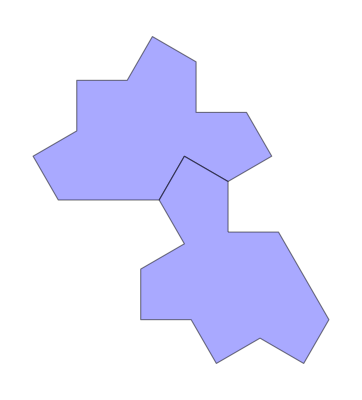
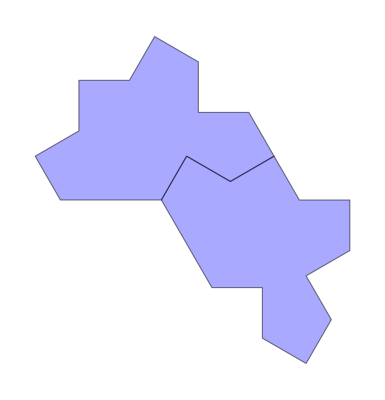
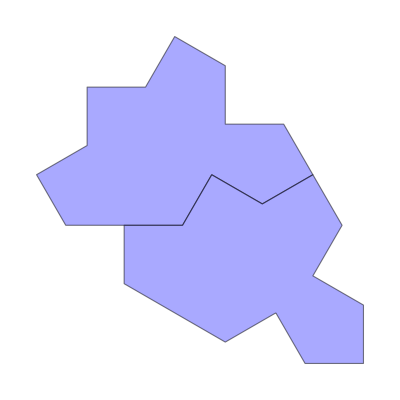
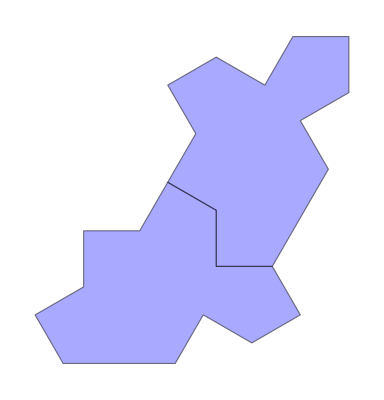
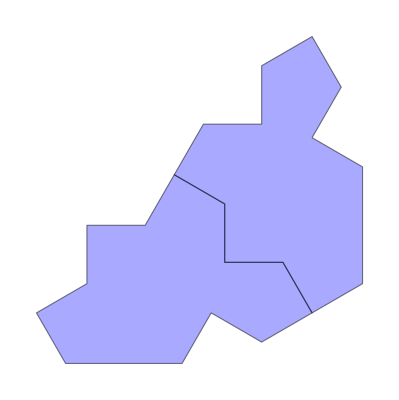
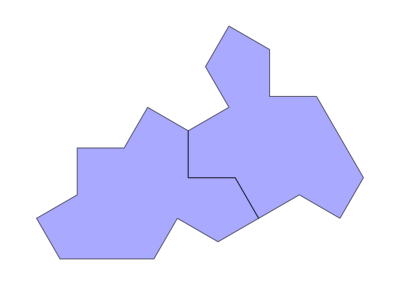
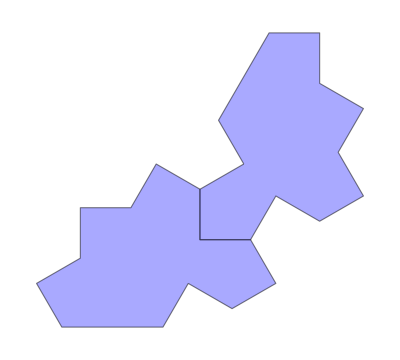

```mathematica
show[Prepend[#,{0,0}]&/@#,step->{1,1}]&/@res2
```

```mathematica
Iconize[res2]
```

# More Eliminations Details

## 1/3+1/3+1/3

```mathematica
init=Prepend[#,{0,0}]&/@oneThirdVertexTheoremLis[{1,1}][[10]];
poly=PolygonListUnion[spectre@@@init]
```

Polygon[…]

```mathematica
res=NestList[
QuietEcho@growForcedPoint[#[[1]],#[[2]],step->{1,1},BranchesNumberLimit->2]&,
init->poly,
2];
```

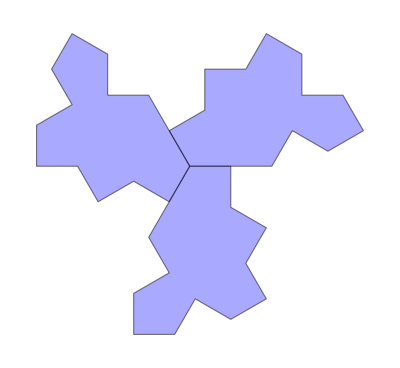
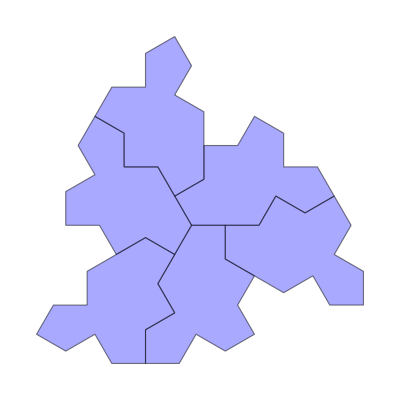
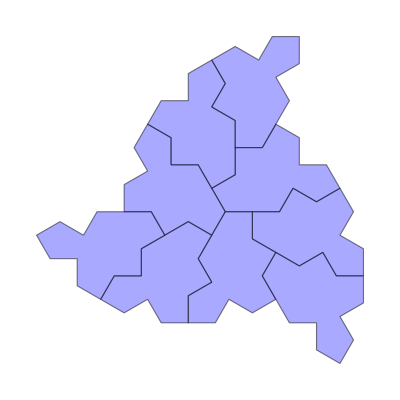

```mathematica
show[#,step->{1,1}]&/@res[[;;3,1]]
```

```mathematica
state=res[[3]];
```

```mathematica
newres=getBranchesOrderedByForce[state[[1]],state[[2]],2,step->{1,1}];
```

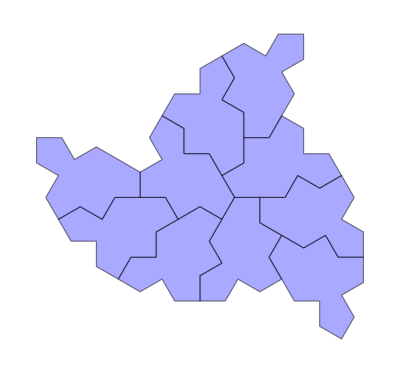
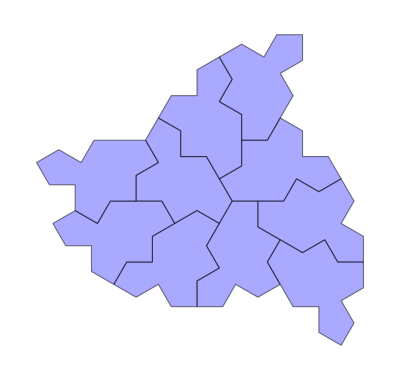
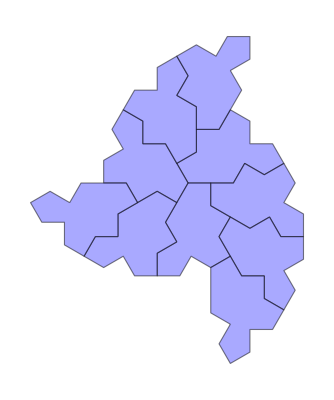
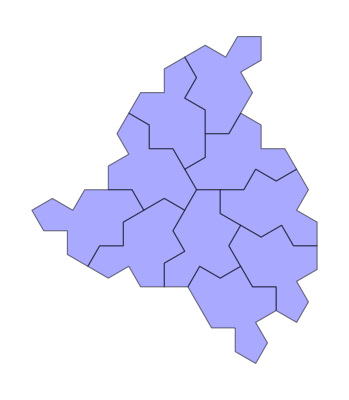
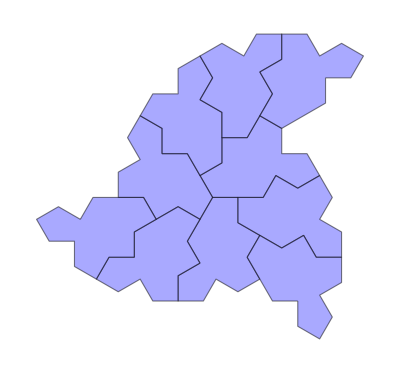
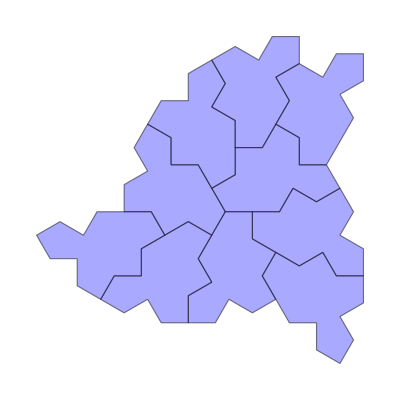
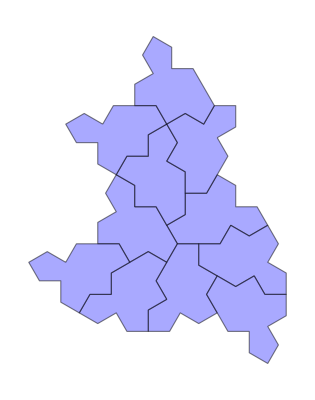
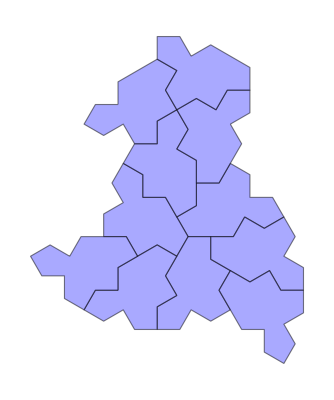
{-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-18}

```mathematica
MapThread[
Labeled[
show[#1,step->{1,1}],
#2]&,
{
newres[[All,1]],
Range[18]
}
]
```

11,12,13,14,15,16 are dead, obviously.

```mathematica
growForcedPoint[newres[[1,1]],newres[[1,2]],step->{1,1}]//QuietEcho
```

Invalid Vertices:{{-2-√3,1}}

{}

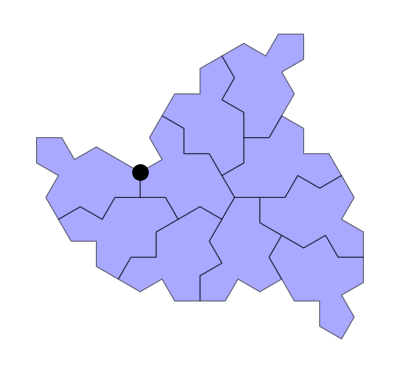

```mathematica
Show[
show[newres[[1,1]],step->{1,1}],
Graphics[{PointSize[0.03],Point[{{-2-√3,1}}]}]
]
```

Dead.

```mathematica
growForcedPoint[newres[[2,1]],newres[[2,2]],step->{1,1}]//QuietEcho
```

Impossible Vertices:{{-2-(√3)/2,3/2+√3}}

{}

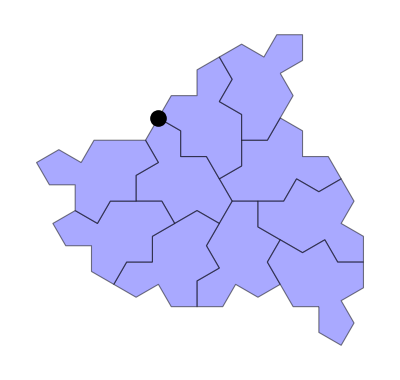

```mathematica
Show[
show[newres[[2,1]],step->{1,1}],
Graphics[{PointSize[0.03],Point[{{-2-(√3)/2,3/2+√3}}]}]
]
```

Dead, too.

Since the first six cases can be divided into two groups, each group is rotation equivalent. So first six cases are proven dead.

For case 7,8,9,10,17,18 can be grouped into {7,9,17} and{8,10,18}, where each group is a equivalent class.

```mathematica
state=newres[[7]];
```

```mathematica
growForcedPoint[state[[1]],state[[2]],step->{1,1}]//QuietEcho
```

{{{0,0},0,False,12},{{0,0},4,False,12},{{0,0},8,False,12},{{-1/2,-(√3)/2},7,False,11},{{-1/2,(√3)/2},3,False,11},{{1,0},11,False,11},{{-1/2-√3,-(√3)/2},6,False,11},{{-1/2+(√3)/2,3/2+(√3)/2},2,False,11},{{1+(√3)/2,-3/2},10,False,11},{{-1/2,3+(3 √3)/2},6,False,11},{{-1/2,3+(3 √3)/2},4,False,9},{{1/2 (-4-√3),1/2 (3+2 √3)},8,False,9}}→Polygon[…]

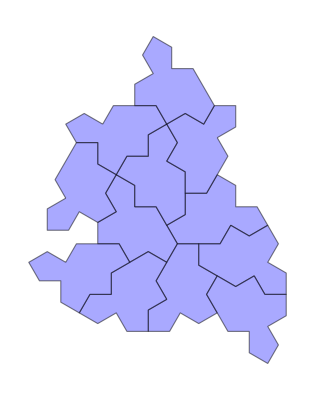

```mathematica
show[{{{0,0},0,False,12},{{0,0},4,False,12},{{0,0},8,False,12},{{-1/2,-(√3)/2},7,False,11},{{-1/2,(√3)/2},3,False,11},{{1,0},11,False,11},{{-1/2-√3,-(√3)/2},6,False,11},{{-1/2+(√3)/2,3/2+(√3)/2},2,False,11},{{1+(√3)/2,-3/2},10,False,11},{{-1/2,3+(3 √3)/2},6,False,11},{{-1/2,3+(3 √3)/2},4,False,9},{{1/2 (-4-√3),1/2 (3+2 √3)},8,False,9}},step->{1,1}]
```

Dead because of the gap.

```mathematica
state=newres[[8]];
```

```mathematica
growForcedPoint[state[[1]],state[[2]],step->{1,1}]//QuietEcho
```

Impossible Vertices:{{1/2 (-3-√3),3/2 (1+√3)},{-2-(√3)/2,3/2+√3},{-2-√3,1+2 √3},{-2-(√3)/2,3/2+2 √3}}

{}

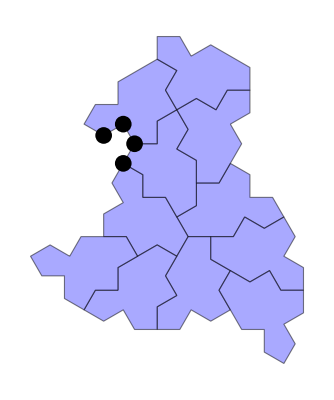

```mathematica
Show[
show[newres[[8,1]],step->{1,1}],
Graphics[{PointSize[0.03],Point[{{1/2 (-3-√3),3/2 (1+√3)},{-2-(√3)/2,3/2+√3},{-2-√3,1+2 √3},{-2-(√3)/2,3/2+2 √3}}]}]
]
```

Dead.

So, this case is dead.

## T

```mathematica
init=Prepend[#,{0,0}]&/@TshapeList[{1,1}][[3]];
poly=PolygonListUnion[spectre@@@init];
```

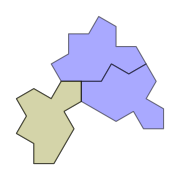

```mathematica
show[init[[{1}]],init,step->{1,1},ImageSize->Small]
```

```mathematica
getVertexInformation[{1,1}][
(spectreVertices@@init[[1]])[[2]],
init
]
```

{{{0,-1},2,False,2},{{0,-1},11,False,12}}

```mathematica
oneThirdVertexTheoremLis[{1,1}][[All,All,3]]
```

{{2,6,6},{2,6,2},{2,2,2},{4,12,4},{4,12,14},{4,12,12},{4,4,4},{6,6,6},{12,14,12},{12,12,12}}

No such configuration as {2,12}

## T

```mathematica
init=Prepend[#,{0,0}]&/@TshapeList[{1,1}][[6]];
```

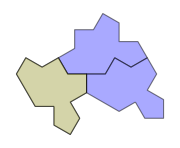

```mathematica
show[init[[{1}]],init,step->{1,1},ImageSize->Small]
```

```mathematica
getVertexInformation[{1,1}][
(spectreVertices@@init[[1]])[[6]],
init
]
```

{{{0,-1},10,False,6},{{0,-1},11,False,12}}

```mathematica
oneThirdVertexTheoremLis[{1,1}][[All,All,3]]
```

{{2,6,6},{2,6,2},{2,2,2},{4,12,4},{4,12,14},{4,12,12},{4,4,4},{6,6,6},{12,14,12},{12,12,12}}

No such configuration as {6,12}

## Update Theorems

Delete the above  configurations in the theorem list.

```mathematica
Quit
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["HappyTile.wl"]
```

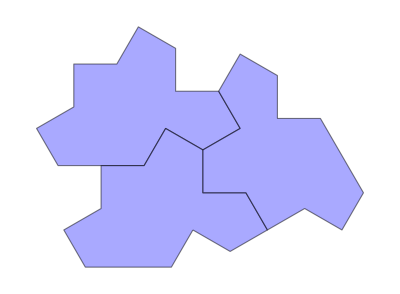
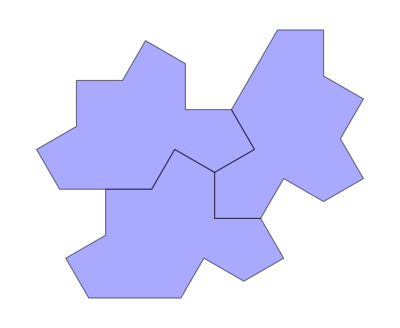
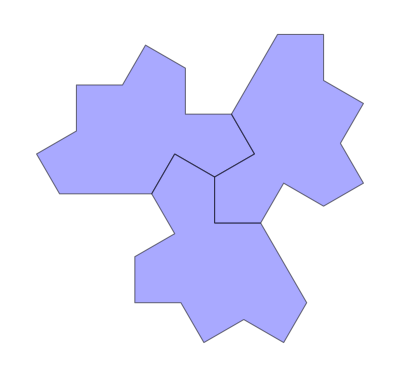
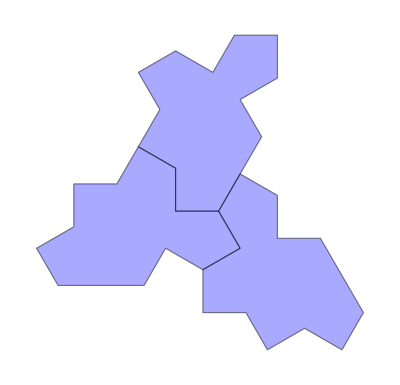
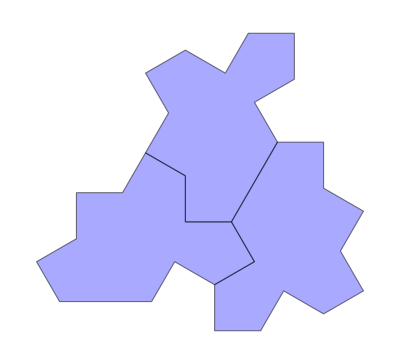
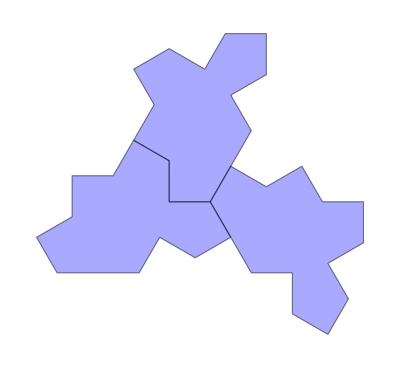
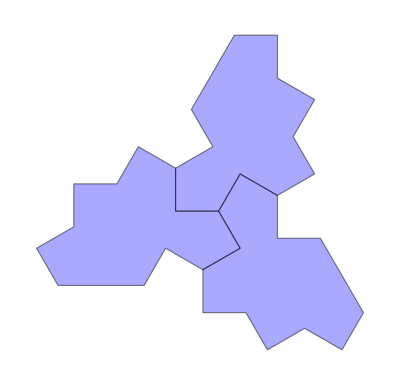
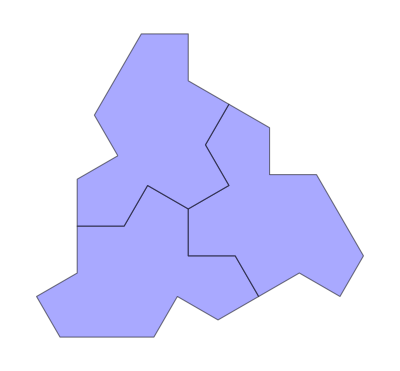

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneThirdVertexTheoremLis[{1,1}],{2}]]
```

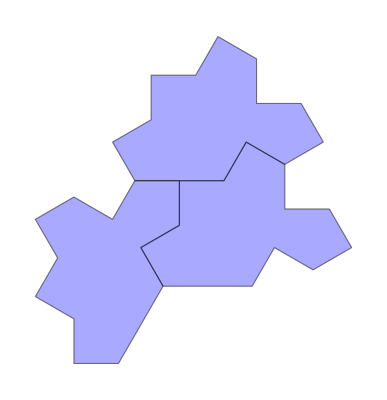
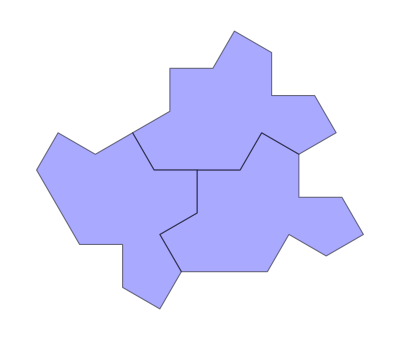
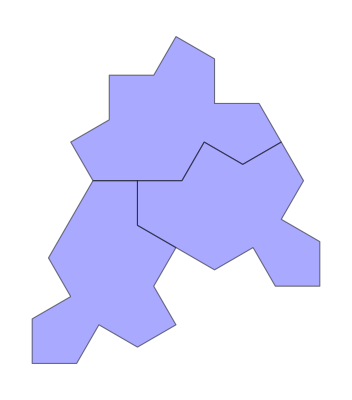
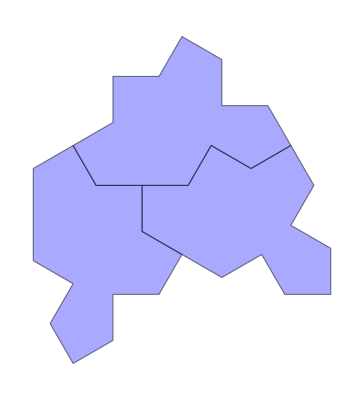

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,TshapeList[{1,1}],{2}]]
```

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneFourthVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Eliminate

```mathematica
init=Prepend[#,{0,0}]&/@oneFourthVertexTheoremLis[{1,1}][[2]];
poly=PolygonListUnion[spectre@@@init];
```

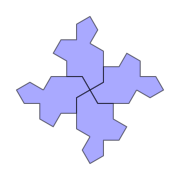

```mathematica
show[init,step->{1,1},ImageSize->Small]
```

```mathematica
res=NestList[
QuietEcho@growForcedPoint[#[[1]],#[[2]],step->{1,1},BranchesNumberLimit->4]&,
init->poly,
3
];
```

Impossible Vertices:{{0,3+√3},{-3-√3,0},{0,-3-√3},{3+√3,0}}

There are four impossible vertices, which means they have branches by theorem, but all eliminated by intersection test.

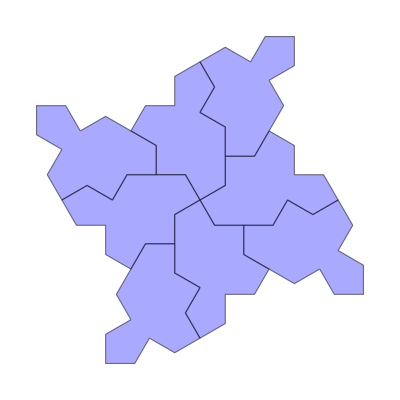
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
show[#,step->{1,1}]&/@res[[;;3,1]]
```

```mathematica
Show[Graphics[{PointSize[0.05],
Point[{{0,3+√3},{-3-√3,0},{0,-3-√3},{3+√3,0}}]}],
show[res[[3,1]],step->{1,1},EdgeForm->Black],ImageSize->Small
]
```

-Graphics-

We can see what happens if we grow on these points:

```mathematica
Union@@generator[{1,1}][res[[3,1]],{0,3+√3}]
```

T

1/4 * 4

{{{{0,3+√3},6,False,11},{{0,3+√3},4,False,9}},{{{0,3+√3},7,False,9},{{0,3+√3},5,False,7}}}

```mathematica
show[#,res[[3,1]],step->{1,1}]&/@{{{{0,3+√3},6,False,11},{{0,3+√3},4,False,9}},{{{0,3+√3},7,False,9},{{0,3+√3},5,False,7}}}
```

{-Graphics-,-Graphics-}

Obvious intersection caused.

## Eliminate

```mathematica
init=Prepend[#,{0,0}]&/@oneFourthVertexTheoremLis[{1,1}][[4]];
poly=PolygonListUnion[spectre@@@init];
```

```mathematica
show[init,step->{1,1},ImageSize->Small]
```

-Graphics-

```mathematica
res=NestList[
QuietEcho@growForcedPoint[#[[1]],#[[2]],step->{1,1},BranchesNumberLimit->4]&,
init->poly,
5
];
```

```mathematica
GraphicsRow[show[#,step->{1,1}]&/@res[[All,1]],ImageSize->Full,Frame->All,FrameStyle->LightGray]
```

-Graphics-

Dead due to the impossible caves.

## Update Theorems

Delete the above  configurations in the theorem list.

```mathematica
Quit
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["HappyTile.wl"]
```

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneThirdVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,TshapeList[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneFourthVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics-

## Eliminate

```mathematica
init=Prepend[#,{0,0}]&/@oneFourthVertexTheoremLis[{1,1}][[1]];
poly=PolygonListUnion[spectre@@@init];
```

```mathematica
res=NestList[
QuietEcho@growForcedPoint[#[[1]],#[[2]],step->{1,1},BranchesNumberLimit->4,InvalidPointsDetect->False]&,
init->poly,
3
];
```

Here I chose not to detect invalid or impossible points to see what happens:

```mathematica
show[#,step->{1,1}]&/@res[[All,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Invalid vertex configuration shows up, and ends.

## Update Theorems

Delete the above  configurations in the theorem list.

```mathematica
Quit
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["HappyTile.wl"]
```

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneThirdVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,TshapeList[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneFourthVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics-

## 1/3+1/3+1/3

```mathematica
init=Prepend[#,{0,0}]&/@oneThirdVertexTheoremLis[{1,1}][[-2]];
poly=PolygonListUnion[spectre@@@init]
```

Polygon[…]

```mathematica
g=growthGraph[init,poly,4,step->{1,1},
GraphLayout->"LayeredDigraphEmbedding"
]
```

-Graphics-

All branches are dead. It is surprising that it is easier to proved invalid for spectre tiles than hat tiles in terms of this vertex configuration.

We can grab all the leaves to see what happened to them:

```mathematica
Grid[
Partition[
show[#,step->{1,1}]&/@VertexList[g][[-9;;,1]],
UpTo[5]
],
Frame->All,FrameStyle->Directive[Red,Dotted]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

All of them have impossible caves.

## Update Theorems

Delete the above  configurations in the theorem list.

```mathematica
Quit
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["HappyTile.wl"]
```

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneThirdVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,TshapeList[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[show[#,step->{1,1}]&/@Map[Prepend[#,{0,0}]&,oneFourthVertexTheoremLis[{1,1}],{2}]]
```

-Graphics--Graphics--Graphics-

## 1/4+1/4+1/4+1/4

```mathematica
init=Prepend[#,{0,0}]&/@oneFourthVertexTheoremLis[{1,1}][[3]];
poly=PolygonListUnion[spectre@@@init];
```

```mathematica
res=NestWhileList[
QuietEcho@growForcedPoint[#[[1]],#[[2]],step->{1,1},BranchesNumberLimit->2,InvalidPointsDetect->True]&,
init->poly,
If[SameQ[#2,{}],False,UnsameQ[#1,#2]]&,
2,
4
];
```

Invalid Vertices:{{1/2 (4+√3),1/2 (3+2 √3)},{-3/2-√3,1/2 (4+√3)},{-2-(√3)/2,-3/2-√3},{3/2+√3,-2-(√3)/2}}

There are four invalid vertices.

```mathematica
show[#,step->{1,1}]&/@res[[;;2,1]]
```

{-Graphics-,-Graphics-}

```mathematica
Show[show[res[[2,1]],step->{1,1},EdgeForm->Black],
Graphics[{PointSize[.05],Point[{{1/2 (4+√3),1/2 (3+2 √3)},{-3/2-√3,1/2 (4+√3)},{-2-(√3)/2,-3/2-√3},{3/2+√3,-2-(√3)/2}}]}
],ImageSize->Small]
```

-Graphics-

It is impossible to tile more on these vertices.

# Conclusion

Here is the conclusion summary, with reflection forbidden:

```mathematica
Column[{
Labeled[
GraphicsGrid[
Partition[
Show[
Graphics[{PointSize[0.1],RandomColor[],Point[{0,0}]}],
show[#,step->{1,1},ChooseColor->{White},EdgeForm->Black]
]&/@Map[Prepend[#,{0,0}]&,oneThirdVertexTheoremLis[{1,1}],{2}],
4],
Frame->All,FrameStyle->Directive[Orange,Dotted,Thick]
],
Style["1/3+1/3+1/3 Vertex Configuration",Purple]
],
Labeled[
GraphicsGrid[
{
Show[
Graphics[{PointSize[0.1],RandomColor[],Point[{0,0}]}],
show[#,step->{1,1},ChooseColor->{White},EdgeForm->Black]
]&/@Map[Prepend[#,{0,0}]&,oneFourthVertexTheoremLis[{1,1}],{2}]
},
Frame->All,FrameStyle->Directive[Orange,Dotted,Thick],AspectRatio->1/4
],
Style["1/4+1/4+1/4+1/4 Vertex Configuration",Red]
],
Labeled[
GraphicsGrid[
{
Show[
Graphics[{PointSize[0.1],RandomColor[],Point[{0,0}]}],
show[#,step->{1,1},ChooseColor->{White},EdgeForm->Black]
]&/@Map[Prepend[#,{0,0}]&,TshapeList[{1,1}],{2}]
},
Frame->All,FrameStyle->Directive[Orange,Dotted,Thick]
],
Style["1/4+1/4+1/2 Vertex Configuration",Gray]
]
}]
```

-Graphics-1/3+1/3+1/3 Vertex Configuration
-Graphics-1/4+1/4+1/4+1/4 Vertex Configuration
-Graphics-1/4+1/4+1/2 Vertex Configuration

All of them show up in the tiling cluster, which means the elimination has been done completely.